```mathematica
(*g=1;*)
thetaB=thetaA  ;
phiB=phiA;
delta=g-(thetaA+g phiA)/(1+1/c);
Ga = g(1-phiB/(1+1/(c-Ca)));
Gb =g(1-phiA/(1+1/(Ca)));
Gw = Ga Gb/g;
Da = delta+thetaB/(1+1/(c-Ca));
Db = delta+thetaA/(1+1/(Ca));
Dw = Da+Db-delta;
Nr = W0/(Dw/Gw-1);
Pd = Pa Da/Ga + (1-Pa)Db/Gb;
Pe = Exp[-m Nr (1-Pd)];
Simplify[Pe]
```

ⅇ^((m (-c (-1+Pa) (1+2 Ca (-1+phiA))+c^2 (-1+Pa) (-1+phiA)+Ca (-1+Ca+2 Pa-Ca phiA)) (g phiA+thetaA) W0)/((c-Ca) Ca (g phiA (-2+c (-1+phiA)+phiA)-(2+c) thetaA)))

```mathematica
Simplify[Solve[D[Pe,Ca]==0,Pa]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Pa→(c-Ca)^2/(c^2-2 c Ca+2 Ca^2)}}

General::munfl: Exp[-24476.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-16317.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

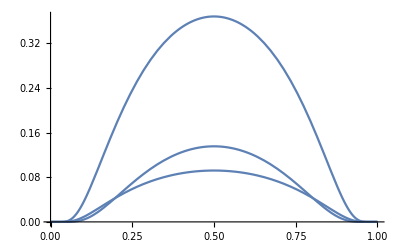

```mathematica
Plot[{ⅇ^((m (Ca+c (-1+Pa)-2 Ca Pa) W0)/((c-Ca) Ca)),ⅇ^((m (c^2 (-1+Pa)+c (-1-2 Ca (-1+Pa)+Pa)-Ca (-1+Ca+2 Pa)) W0)/((2+c) (c-Ca) Ca)),
ⅇ^(-m W0((1-Pa)/(Ca(1+(1+Ca)/(2-Ca)))+Pa/((1-Ca)(1+(2-Ca)/(1+Ca)))))*0.25}/.{m->1,W0->1,Pa->0.5,c->1},{Ca,0,1}]
```

(c-c Pa-√(-c^2 (-1+Pa) Pa (-1+c (-1+phiA)) (-1+c (-1+phiB)))+c^2 (-1+Pa) (-1+phiB))/(1+c-2 Pa-c phiB+c Pa (-2+phiA+phiB))

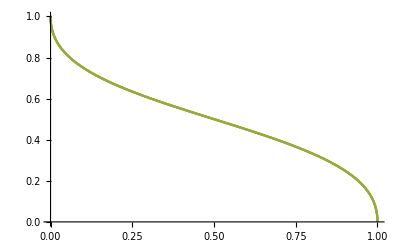

```mathematica
y=(c-c Pa-√(-c^2 (-1+Pa) Pa (-1+c (-1+phiA)) (-1+c (-1+phiB)))+c^2 (-1+Pa) (-1+phiB))/(1+c-2 Pa-c phiB+c Pa (-2+phiA+phiB))
Plot[{y/.{phiA->0.9,phiB->0.9,c->1},
y/.{phiA->0.5,phiB->0.5,c->1},
1/(1+√(Pa/(1-Pa))),
},{Pa,0,1}]
```

```mathematica
Simplify[y/c/.{phiA->1,phiB->1}]
```

(c (-1+Pa)+√(-c^2 (-1+Pa) Pa))/(c (-1+2 Pa))

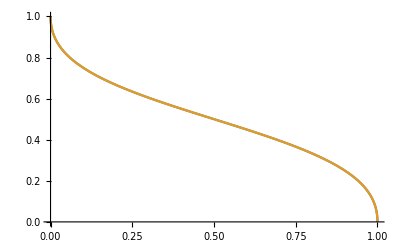

```mathematica
Plot[{(1- Pa-√((1-Pa) Pa))/(1-2  Pa), 1/(1+√(Pa/(1-Pa)))},{Pa,0,1}]
```

```mathematica
theta = g(1+1/c);
Da = theta/(1+1/(c-Ca));
Db = theta/(1+1/(Ca));
Dw = Da+Db;
Nr = W0/(1-Dw/g);
Pd = (Pa Da + (1-Pa) Db)/g;
Pe = Exp[-m Nr (1-Pd)];
Simplify[Pe]
Simplify[Solve[D[Pe,Ca]==0,Pa]]

delta=g(1- 1/(1+1/c));
Ga = g(1-1/(1+1/(c-Ca)));
Gb =g(1-1/(1+1/(Ca)));
Gw = Ga Gb/g;
Nr = W0/(1-delta/Gw);
Pd = delta(Pa /Ga + (1-Pa)/Gb);
Pe = Exp[-m Nr (1-Pd)];
Simplify[Pe]

g=1;
theta = 1-phi;
delta=g(1- 1/(1+1/c));
Ga = g(1-phi/(1+1/(c-Ca)));
Gb =g(1-phi/(1+1/(Ca)));
Gw = Ga Gb/g;
Da = delta+theta/(1+1/(c-Ca));
Db = delta+theta/(1+1/(Ca));
Dw = Da+Db-delta;
Nr = W0/(1-Dw/Gw);
Pd = Pa Da/Ga + (1-Pa)Db/Gb;
Pe = Exp[-m Nr (1-Pd)];
Simplify[Pe]
```